# Values for τα

## scattering function

## N=4096

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassAging/fluidConfigurations/scatteringFunction_N4096_TEq0.10000000_p3.80000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
plist={3.75, 3.8 ,3.825 ,3.85, 3.9, 4.0};
pstring=ToString[NumberForm[#,{9,5},ExponentFunction->(Null&)]]&/@plist
```

{3.75000,3.80000,3.82500,3.85000,3.90000,4.00000}

```mathematica
sk4096=Table[Table[Import["/home/chengling/Research/Project/Cell/glassAging/fluidConfigurations/scatteringFunction_N4096_TEq0.10000000_p"<>pstring[[p]]<>"_idx"<>ToString[id]<>".nc","Data"],{id,0,19}],{p,Length[plist]}];
```

```mathematica
Normal[sk4096[[5,15,2,1]]]
```

0.0134008

```mathematica
0.14726215563702155
```

```mathematica
0.14726215563702155
```

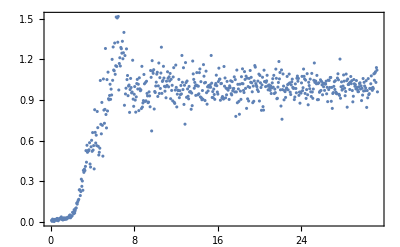

```mathematica
ListPlot[Table[{test[[1,i]],test[[2,i]]},{i,Length[test[[1]]]}]]
```

```mathematica
sk=Table[Table[{sk4096[[p,1,1]][[t]],Mean[Table[sk4096[[p,id,2]][[t]],{id,20}]]},{t,Length[sk4096[[p,1,1]]]}],{p,Length[plist]}];
```

```mathematica
sk[[3,110]]
```

{5.49779,0.951295}

```mathematica
Table[ListPlot[Table[{sk4096[[p,1,1]][[t]],Mean[Table[sk4096[[p,id,2]][[t]],{id,20}]]},{t,Length[sk4096[[p,1,1]]]}],PlotStyle->redBluePlotConfig[6][[7-p]],PlotLegends->StringJoin["p=",ToString[plist[[p]]]],FrameLabel->{"k","S(k)"},ImageSize->600,PlotMarkers->Automatic,PlotRange->{{0,10},All},Joined->True],{p,Length[plist]}]
```

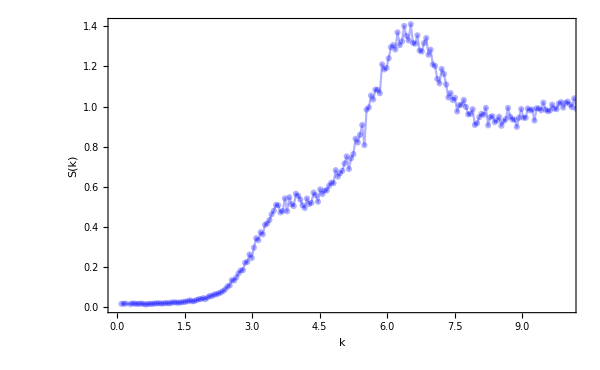
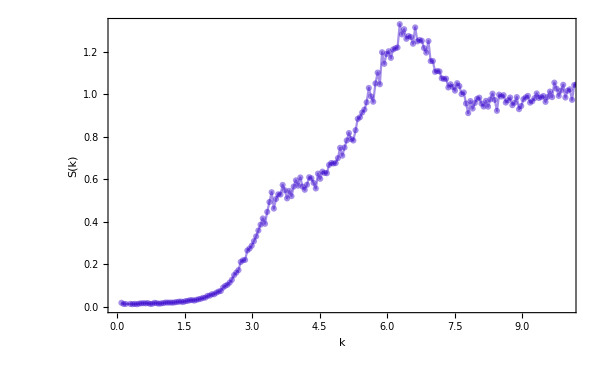
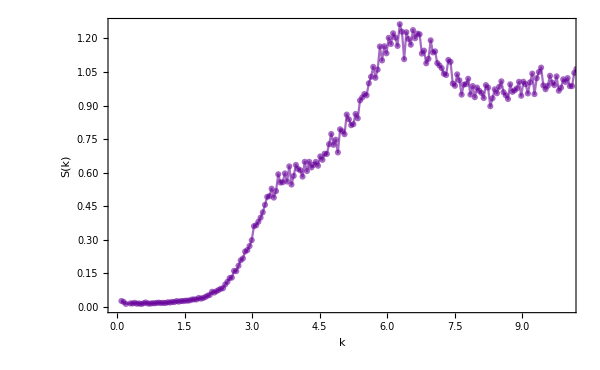
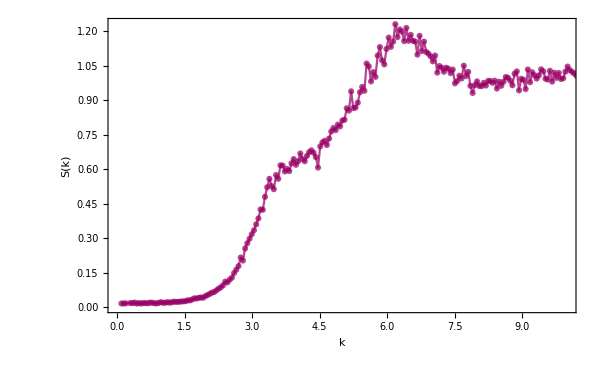
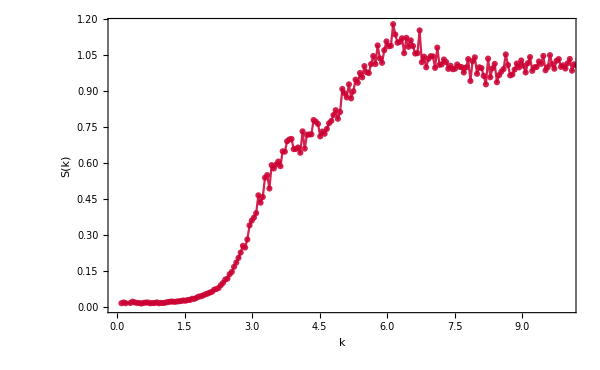
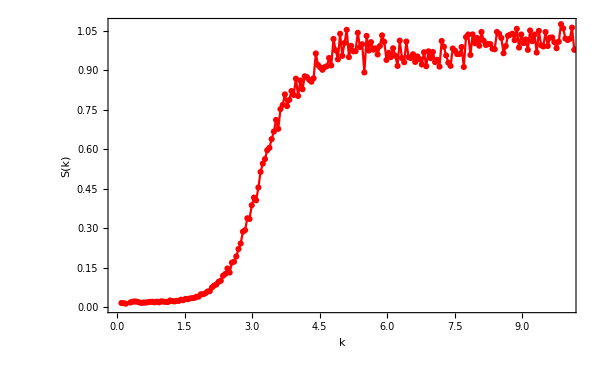

```mathematica
klist={6.55,6.50,6.40,6.35,6.30,5.35};
```

### tauAlpha for bidispers

```mathematica
tauAlphaBiP380={{0.002, 15869.323},{0.0025, 8923.9646},{0.0031, 5018.3166},{0.00385, 2822.0078000000003},{0.00475, 1780.5616},{0.006, 1001.2898},{0.0075, 631.7722},{0.009, 398.626},{0.0115, 251.50620000000004},{0.0125, 224.15599999999998},{0.014, 178.06599999999997},{0.0175, 112.33779999999999},{0.0215, 70.8828},{0.027, 50.1854},{0.033, 35.5214},{0.041, 25.152600000000003},{0.05, 17.8006},{0.065, 11.2278},{0.08, 7.9514},{0.095, 6.313199999999999},{0.12, 4.475200000000001},{0.15, 3.1565999999999996}};
```

```mathematica
tauAlphaBiP385={{0.0007, 19978.25},{0.00085, 14143.502},{0.00105, 7953.4812},{0.0013, 5630.6302000000005},{0.0016, 3552.6921999999995},{0.002, 2241.5996},{0.0025, 1586.9324},{0.0031, 1123.4569999999999},{0.00385, 795.3539999999999},{0.00475, 563.067},{0.006, 398.626},{0.0075, 282.1928},{0.009, 199.78260000000003},{0.0115, 141.4262},{0.0125, 126.0626},{0.014, 100.131},{0.0175, 70.8828},{0.0215, 50.1854},{0.027, 35.5214},{0.033, 28.229200000000002},{0.041, 19.9782},{0.05, 14.1446},{0.065, 10.0092},{0.08, 7.092199999999998},{0.095, 5.6338},{0.12, 3.9956},{0.15, 2.8169999999999997}};
```

```mathematica
tauAlphaBiP375={{0.00475, 17805.616},{0.006, 7088.543000000001},{0.0075, 2822.0078000000003},{0.009, 1414.3602},{0.0115, 631.7722},{0.0125, 501.8336},{0.014, 355.2732},{0.0175, 199.78260000000003},{0.0215, 126.0626},{0.027, 70.8828},{0.033, 44.7312},{0.041, 31.665599999999998},{0.05, 22.415599999999998},{0.065, 12.6062},{0.08, 8.9302},{0.095, 7.092199999999998},{0.12, 4.475200000000001},{0.15, 3.1565999999999996}};
```

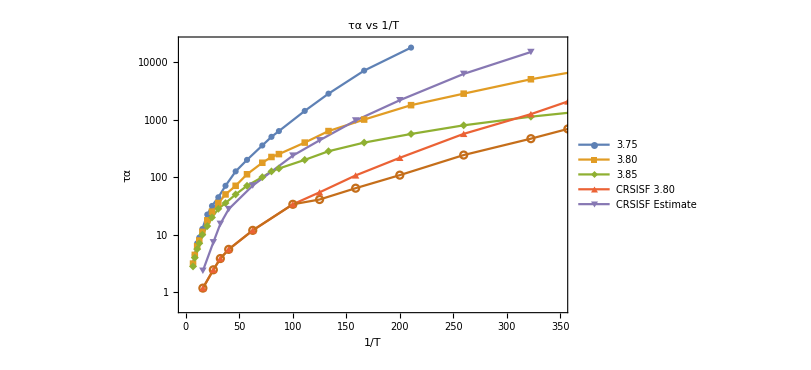

```mathematica
ListLogPlot[{Table[{1/tauAlphaBiP375[[T,1]],tauAlphaBiP375[[T,2]]},{T,Length[tauAlphaBiP375]}],Table[{1/tauAlphaBiP380[[T,1]],tauAlphaBiP380[[T,2]]},{T,Length[tauAlphaBiP380]}],Table[{1/tauAlphaBiP385[[T,1]],tauAlphaBiP385[[T,2]]},{T,Length[tauAlphaBiP385]}],Table[{1/T[[T]],tauEsGeneral[[T]]},{T,Length[tauEsGeneral]}],Table[{1/TlistGeneral[[T]],tauEs375[[T]]},{T,11}],Table[{1/TlistGeneral[[T]],tauEs385[[T]]},{T,Length[tauEsGeneral]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"3.75","3.80","3.85","CRSISF 3.80","CRSISF Estimate"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->{{0,350},All}]
```

```mathematica
N[1/0.003371]
```

296.648

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.0028,0.0025,0.0022,0.002,0.0018};
```

```mathematica
tauCRSISFAllT={0.7285373853764064,1.4152404775702498,1.613886208267606,2.6928959118149005,4.036978269867807,5.211288667943124,9.195220854118805,9.51447666455108,14.8936042282918,25.979282824258807,32.334383768865926,138.2556108073841,1036.0214627589678,1239.2236650915565,2019.5435505092169,2804.795879299683,4144.731734954942,5262.525888586673,6834.041719690315,9346.072932809862,13224.128435539176,18754.26826593246,19569.09754005547};
```

```mathematica
Tlist={0.08868,0.05586,0.05409,0.03756,0.03105,0.02652,0.01945,0.01782,0.01471,0.01141,0.01023,0.005873,0.003371,0.00309559,0.00285428,0.00264787,0.00246931,0.0023133,0.00222222,0.00210526,0.002,0.00190476,0.00181818};
```

```mathematica
tauEs375=Table[tauEsGeneral[[T]]*(1+T),{T,11}]
```

{2.36823,7.38854,15.4602,27.8707,71.549,236.674,436.609,965.658,2169.66,6218.51,14927.3}

```mathematica
tauEs385=Join[Table[tauEsGeneral[[T]],{T,5}],Table[tauEsGeneral[[T]]/(T-3)*3,{T,6,16}]]
```

{1.18412,2.46285,3.86506,5.57413,11.9248,33.8105,40.9321,64.3772,108.483,242.28,466.479,688.333,1119.4,1909.09,3221.3,5076.92}

```mathematica
NumberForm[#,{9,2},ExponentFunction->(Null&)]&/@tauEsGeneral
```

{1.18,2.46,3.87,5.57,11.92,33.81,54.58,107.30,216.97,565.32,1243.95,2065.00,3731.35,7000.00,12885.22,22000.00}

```mathematica
NumberForm[#,{9,2},ExponentFunction->(Null&)]&/@tauEs375
```

{2.37,7.39,15.46,27.87,71.55,236.67,436.61,965.66,2169.66,6218.51,14927.34}